```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

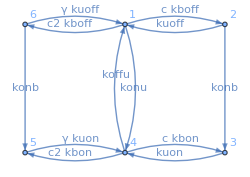

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
var[a_, pss_, Z_]:=(a*pss).(Z.a);
```

```mathematica
kmax =5.;
kmin=0.00001;
kdl=0.0888;
rates={c->1,c2->0,γ->10,konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax};

With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[ss2]]
```

{0.05,0.025,0.175,0.15,0.525,0.075}

```mathematica
a = {0,0,1,1,1,0};
pss = Simplify[ss2];
pion =pss.a;
With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[pion]]
```

0.85

```mathematica
Pss = Table[pss, {i,1,Length[pss]}];
```

```mathematica
Z = Inverse[Pss - Q2] - Pss;
With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[2*var[a,pss,Z]]]
```

0.21849999999999986

```mathematica
dpion = D[pion, c];
s = FullSimplify[c*dpion];
```

```mathematica
With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[s]]
```

0.02375

```mathematica
dc = c/100;
iracc= s^2 / var[a,pss,Z];
With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[iracc]]
```

0.005163043478260874

{c kboff1,kuoff1,c kboff2,kuoff2,c kboff3,kuoff3,c kboff4,kuoff4,c kboff5,kuoff5,c kboff6,kuoff6,c kbon1,kuon1,c kbon2,kuon2,c kbon3,kuon3,c kbon4,kuon4,c kbon5,kuon5,c kbon6,kuon6,kon1,koff1,kon2,koff2,kon3,koff3,kon4,koff4,kon5,koff5,kon6,koff6,kon7,koff7}

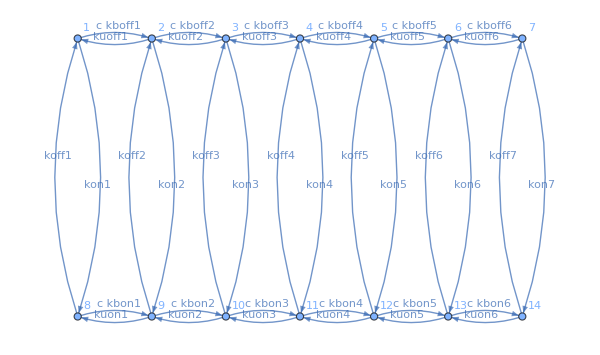

```mathematica
(*Edge lists and weights*)
edges6={{1,2},{2,1},{2,3},{3,2},{3,4},{4,3},{4,5},{5,4},{5,6},{6,5},{6,7},{7,6},{8,9},{9,8},{9,10},{10,9},{10,11},{11,10},{11,12},{12,11},{12,13},{13,12},{13,14},{14,13},{1,8},{8,1},{2,9},{9,2},{3,10},{10,3},{4,11},{11,4},{5,12},{12,5},{6,13},{13,6},{7,14},{14,7}};
weights6 = {c*kboff1,kuoff1,c*kboff2,kuoff2,c*kboff3,kuoff3,c*kboff4,kuoff4,c*kboff5,kuoff5,c*kboff6,kuoff6,c*kbon1,kuon1,c*kbon2,kuon2,c*kbon3,kuon3,c*kbon4,kuon4,c*kbon5,kuon5,c*kbon6,kuon6,kon1,koff1,kon2,koff2,kon3,koff3,kon4,koff4,kon5,koff5,kon6,koff6,kon7,koff7}
nstates6 = 14;
nedges6= Length[edges6];

(*Plot the circuit*)
ClearAll[edgeList];
edgeList=Table[edges6[[i,1]]->edges6[[i,2]],{i,1,nedges6}];
g=Graph[edges6,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights6)[[i]],0.55],{i,1,nedges6}],ImageSize->600, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{8,1},{9,2},{10,3},{11,4},{12,5},{13,6},{14,7}}}]
```

```mathematica
ClearAll[c];
Q6 = RateMatrix[edges6, weights6, nstates6];
ss6 = SteadyStateProbabilities[Q6];
```

```mathematica
Simplify[ss6[[1]]]
```

$Aborted

```mathematica
a6={0,0,0,0,0,0,0,1,1,1,1,1,1,1};
Pss = Table[ss6, {i,1,Length[ss6]}];
Z6 = Inverse[Pss - Q6] - Pss;
```

$Aborted

```mathematica
pion6 = a6.ss6;
dpion = D[pion6, c];
s = Simplify[c*dpion6];
```

```mathematica
iracc= s6^2 / var[a6,ss6,Z6]
```